```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]]
```

C:\Users\shiyi\work\git\work\critical_region\cheby\LPA\v4\scaling\initial_v1\anum51\CP\mubT\buffer

```mathematica
list0=Flatten[Import["a.dat"]];
list=Flatten[Import["b.dat"]];
```

```mathematica
list1=Rest[list0];
list2=Rest[list];
```

```mathematica
ρmin=0;
ρmax=30000;
c0=1.85*10^6;
fpi=93.5;
cmax=10.^7;
cmin=10.^-2;
```

```mathematica
rhoend=80;
eqn6=Table[Evaluate[(test=SetPrecision[Sum[list1[[n]]*Cos[n*ArcCos[(2ρ-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,50}]+1/2 First[list1],52])],{ρ,0,rhoend,rhoend/300}];
eqn7=Table[Evaluate[(test=SetPrecision[Sum[list2[[n]]*Cos[n*ArcCos[(2ρ-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,50}]+1/2 First[list],52])],{ρ,0,rhoend,rhoend/300}];
sigma=Table[√(2 rho),{rho,0,rhoend,rhoend/300}];
```

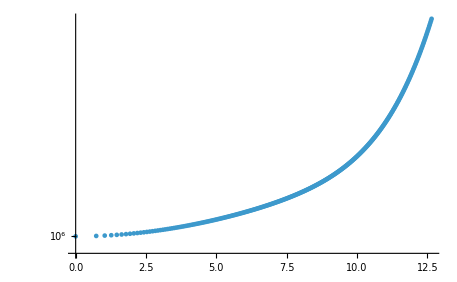

```mathematica
ListPlot[Transpose[{sigma,eqn6-eqn6[[1]]+10^6}],PlotRange->{All,All},ScalingFunctions->{Automatic,"Log"}]
```

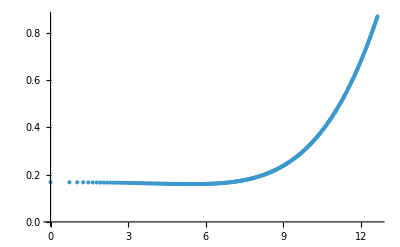

```mathematica
ListPlot[Transpose[{sigma,eqn7}],PlotRange->{All,All},ScalingFunctions->{Automatic,Automatic}]
```